## Setup Distributions

Define the semicircle distribution, Gaussian distribution and Marchenko–Pastur distribution

```mathematica
S=SingFun[1/π&,Line[{-Sqrt[2],Sqrt[2]}],{1/2,1/2}];
G=LFun[Exp[-#^2]/Sqrt[π]&,RealLine,81];
MP=MarchenkoPastur[1.,.1];
```

Define 2 equilibrium measures

```mathematica
Qu=EquilibriumMeasure[#^4&];
Ex=EquilibriumMeasure[Exp[#]-#&];
```

We plot the measures

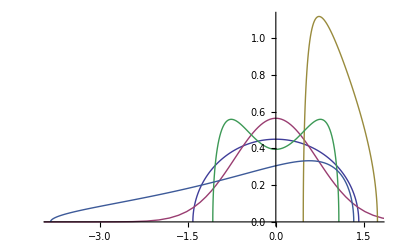

```mathematica
LinePlot[{S,G,MP,Qu,Ex}]
```

## Distribution Histograms

emA is the semicircle distribution

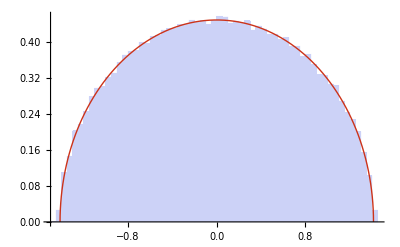

```mathematica
HistogramPlot[RandomSymmetric[300],S]
```

G is the Gaussian distribution

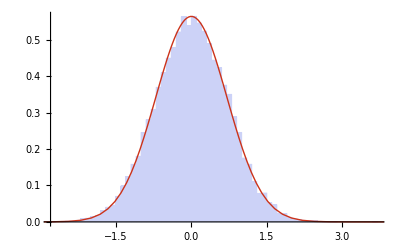

```mathematica
n=150;
HistogramPlot[(Q=RandomOrthogonal[n];Λ=DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]];
Q.Λ.Transpose[Q]),G]
```

MP is the Marchenko–Pastur distribution

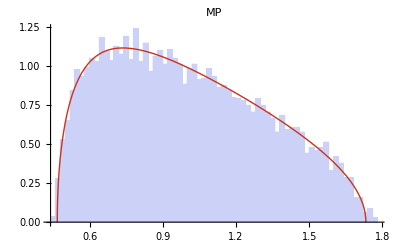

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.Transpose[A]),MP,PlotLabel->"MP"]
```

## Square Root FreePlus Examples

Free probability add SC with itself.  Returns another function of the form  SingFun[fun,{1/2,1/2}]

```mathematica
SS=S~FreePlus~S;
```

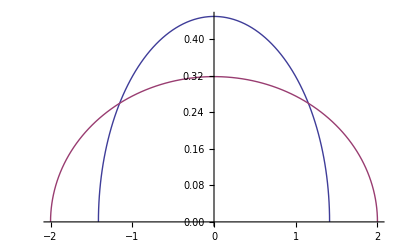

```mathematica
LinePlot[{S,SS}]
```

We can check the RTransforms agree

```mathematica
RTransform[SS,.1 I]-2RTransform[S,.1 I]
```

0.-1.77636×10^-14 ⅈ

We can compare against the histogram:

Free probability add A and B (don’t worry about the warnings)

```mathematica
SQu=S~FreePlus~Qu;
```

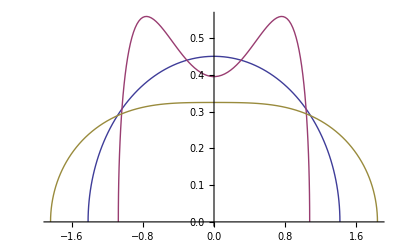

```mathematica
LinePlot[{S,Qu,SQu}]
```

We can check the RTransforms agree

```mathematica
RTransform[SQu,.1 I]-(RTransform[S,.1 I]+RTransform[Qu,.1 I])
```

1.32986×10^-13-1.04805×10^-13 ⅈ

Free probability add A and C

```mathematica
SEx=S~FreePlus~Ex;
```

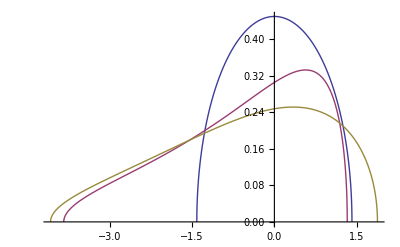

```mathematica
LinePlot[{S,Ex,SEx}]
```

We can check the RTransforms agree

```mathematica
RTransform[SEx,.1 I]-(RTransform[S,.1 I]+RTransform[Ex,.1 I])
```

-2.75557×10^-13+2.07834×10^-13 ⅈ

We can add the semi circle to Marchenko–Pastur distribution

```mathematica
SMP=S~FreePlus~MP;
```

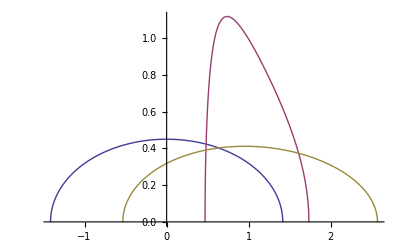

```mathematica
LinePlot[{S,MP,SMP}]
```

### Histograms

We verify the semicircle ⊕ semicircle

OptionValue::nodef: Unknown option "PlotLabel" for SampleRate → 100.

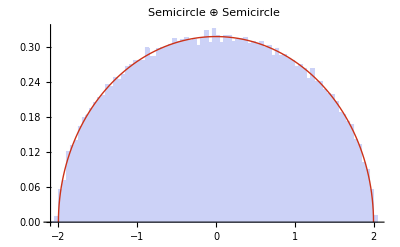

```mathematica
n=300;
HistogramPlot[(
A=RandomSymmetric[n];
B=RandomSymmetric[n];
A+B),SS,PlotLabel->"Semicircle ⊕ Semicircle"]
```

Here we verify the free addition of a  Marchenko–Pastur distribution with a semicircle

OptionValue::nodef: Unknown option "PlotLabel" for SampleRate → 100.

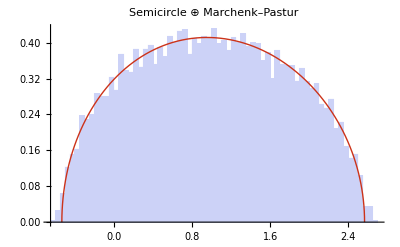

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
B=RandomSymmetric[m];
A.Transpose[A]+B),SMP,PlotLabel->"Semicircle ⊕ Marchenk–Pastur"]
```

## Gaussian FreePlus Examples

Gaussian examples (limited sample points means the accuracy won’t be quite as high here).

```mathematica
GG=G~FreePlus~G;
```

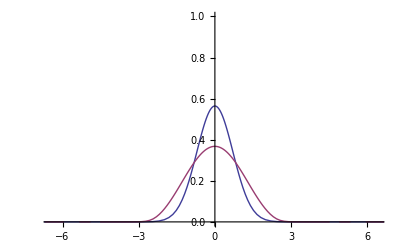

```mathematica
LinePlot[{G,GG},PlotRange->{0,1}]
```

```mathematica
RTransform[GG,.1 I]-(RTransform[G,.1 I]+RTransform[G,.1 I])
```

7.60469×10^-14-9.79181×10^-11 ⅈ

```mathematica
GS=G~FreePlus~S;
```

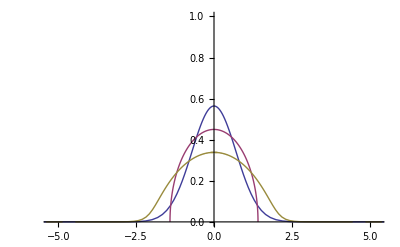

```mathematica
LinePlot[{G,S,GS},PlotRange->{0,1}]
```

```mathematica
GQu=G~FreePlus~Qu;
```

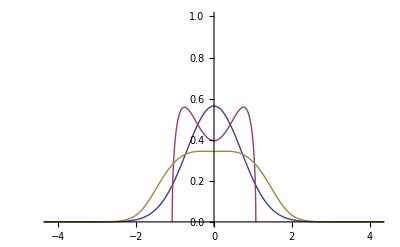

```mathematica
LinePlot[{G,Qu,GQu},PlotRange->{0,1}]
```

```mathematica
MPG=MP~FreePlus~G;
```

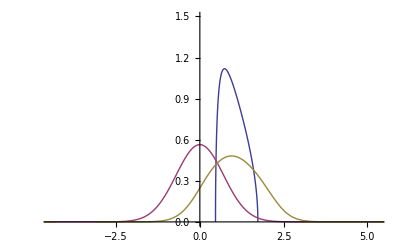

```mathematica
LinePlot[{MP,G,MPG},PlotRange->{0,1.5}]
```

### Histograms

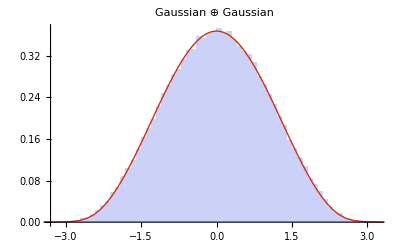

```mathematica
n=300;
HistogramPlot[(
Q=RandomOrthogonal[n];
A=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
Q=RandomOrthogonal[n];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
A+B),GG,PlotLabel->"Gaussian ⊕ Gaussian"]
```

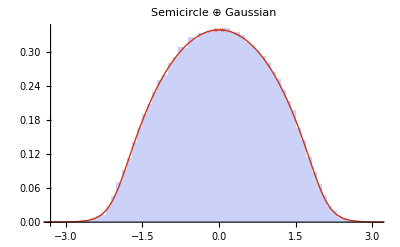

```mathematica
n=300;
HistogramPlot[(
A=RandomSymmetric[n];
Q=RandomOrthogonal[n];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],n]].Transpose[Q];
A+B),GS,PlotLabel->"Semicircle ⊕ Gaussian"]
```

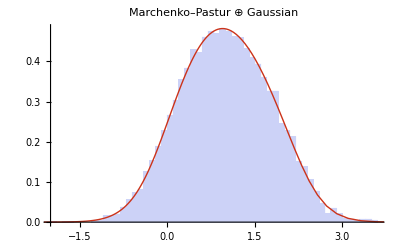

```mathematica
m=70;n=10 m;
HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
B=Q.DiagonalMatrix[RandomVariate[NormalDistribution[0,1/Sqrt[2]],m]].Transpose[Q];
A.Transpose[A]+B),MPG,PlotLabel->"Marchenko–Pastur ⊕ Gaussian"]
```

## Finite n FreePlus Examples

We construct a counting measure which approximates the semicircle

```mathematica
n=50;Sn=PFun[{1/n},Point[#]]&/@((A=RandomSymmetric[n])//Eigenvalues);
```

There Stieljes transforms are close:

```mathematica
Stieljes[Sn,1. I]-Stieljes[S,1.I]
```

-0.00163015+0.000696928 ⅈ

We construct an approximation of the Stieljes function on an ellipse:

```mathematica
ESn=LFun[1/(-2π I)Stieljes[Sn,#]&,Ellipse[{-Sqrt[2],Sqrt[2]},.8 ],150];
```

It’s Stieljes transform is identical to Sn (unless we are very unlucky with the eigenvalues of A!):

```mathematica
Stieljes[Sn,1. I]-Stieljes[ESn,1. I]
```

-8.0231×10^-18-4.44089×10^-16 ⅈ

We compute the FreePlus (can take a while)

```mathematica
SSn=S~FreePlusNewton~ESn;
```

It matches the true measure very closely:

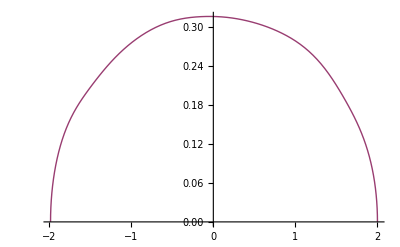

```mathematica
LinePlot[{SS,SSn}]
```

We repeat the experiment with large n

```mathematica
n=500;Sn=PFun[{1/n},Point[#]]&/@(RandomSymmetric[n]//Eigenvalues);
ESn=LFun[1/(-2π I)Stieljes[Sn,#]&,Ellipse[{-Sqrt[2],Sqrt[2]},.8 ],150];
```

```mathematica
SSn=S~FreePlusNewton~ESn;
```

Set::shape: Lists {Private`xia$18413, Private`xib$18413} and Which[{-Im[Power[« 2 »]]/2\ π - Im[Power[« 2 »]]/2\ π + Re[1/Plus[« 2 »]^2], -Im[Power[« 2 »]]/2\ π - Im[Power[« 2 »]]/2\ π + Re[1/Plus[« 2 »]^2]} < 0 && {-Im[Power[« 2 »]]/2\ π - Im[Power[« 2 »]]/2\ π + Re[1/Plus[« 2 »]^2], -Im[Power[« 2 »]]/2\ π - Im[Power[« 2 »]]/2\ π + Re[1/Plus[« 2 »]^2]} < 0, « 6 », {Private`Bisection[Private`GABD$18409, {Private`oa$18413, -0.001}], Private`Bisection[Private`GABD$18409, {0.001, Private`ob$18413}]}] are not the same shape.

$Aborted

Now they agree a lot more:

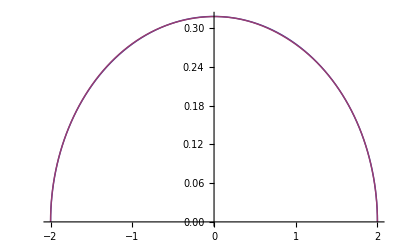

```mathematica
LinePlot[{SS,SSn}]
```

## FreeTimes Examples

We need a  measure supported on the positive real line.  Here we shift the semi circle

```mathematica
Sh=EquilibriumMeasure[(#-3)^2&];
```

```mathematica
ShxSh=Sh~FreeTimes~Sh;
```

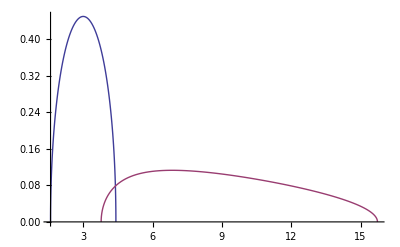

```mathematica
LinePlot[{Sh,ShxSh},PlotRange->All]
```

```mathematica
ShxMP=Sh~FreeTimes~MP;
```

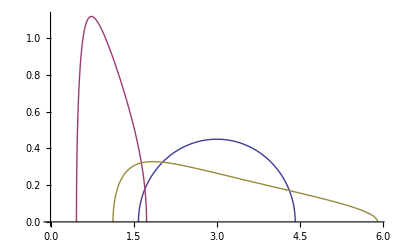

```mathematica
LinePlot[{Sh,MP,ShxMP}]
```

### Histograms

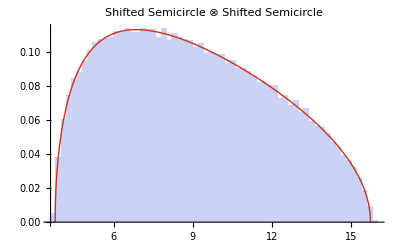

```mathematica
n=300;
HistogramPlot[(
A2=RandomSymmetric[n]+3 IdentityMatrix[n];
A=MatrixPower[A2,1/2];
B=RandomSymmetric[n]+3 IdentityMatrix[n];
A.B.A),ShxSh,PlotLabel->"Shifted Semicircle ⊗ Shifted Semicircle"]
```

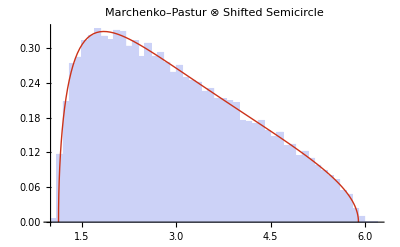

```mathematica
m=100;n=10 m;
HistogramPlot[(
A2=RandomSymmetric[m]+3 IdentityMatrix[m];
A=MatrixPower[A2,1/2];
B=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
A.B.Transpose[B].A),ShxMP,PlotLabel->"Marchenko–Pastur ⊗ Shifted Semicircle"]
```

## FreeCompress Examples

```mathematica
S2=FreeCompress[S,.2];
S4=FreeCompress[S,.4];
S8=FreeCompress[S,.8];
```

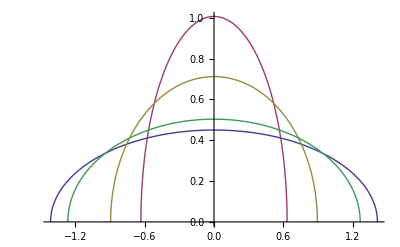

```mathematica
LinePlot[{S,S2,S4,S8}]
```

```mathematica
Qu2=FreeCompress[Qu,.2];
Qu4=FreeCompress[Qu,.4];
Qu8=FreeCompress[Qu,.8];
```

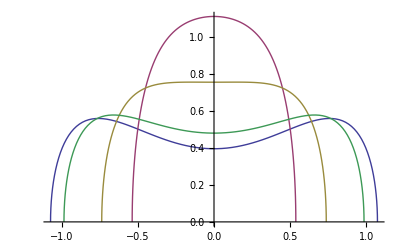

```mathematica
LinePlot[{Qu,Qu2,Qu4,Qu8}]
```

```mathematica
Ex2=FreeCompress[Ex,.2];
Ex4=FreeCompress[Ex,.4];
Ex8=FreeCompress[Ex,.8];
```

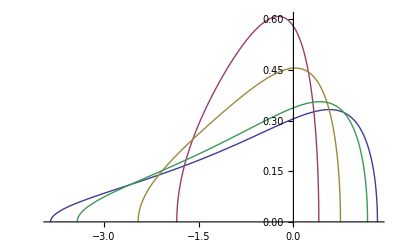

```mathematica
LinePlot[{Ex,Ex2,Ex4,Ex8}]
```

```mathematica
MP2=FreeCompress[MP,.2];
MP4=FreeCompress[MP,.4];
MP8=FreeCompress[MP,.8];
```

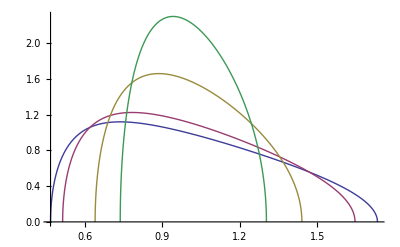

```mathematica
LinePlot[{MP,MP8,MP4,MP2}]
```

The compression of a Marchenko–Pastur distribution is another Marchenko–Pastur distribution:

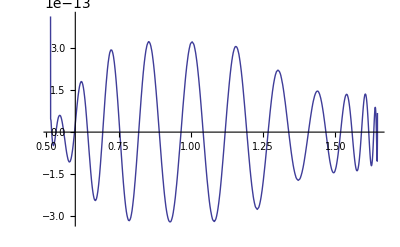

```mathematica
Plot[MarchenkoPastur[MP8//Domain][x]-MP8[x]//Evaluate,{x,0.,2.},PlotRange->All]
```

Now for the Gaussian example.

```mathematica
G2=FreeCompress[G,.2];
G4=FreeCompress[G,.4];
G8=FreeCompress[G,.8];
```

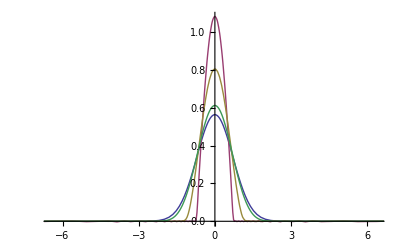

```mathematica
LinePlot[{G,G2,G4,G8}]
```

### Histograms

We can compare with histograms

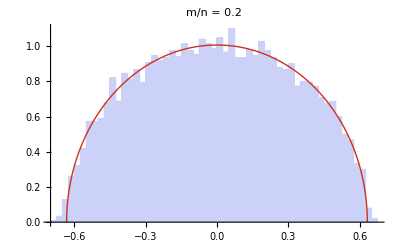

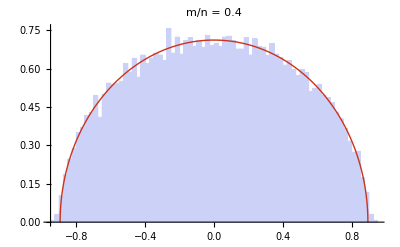

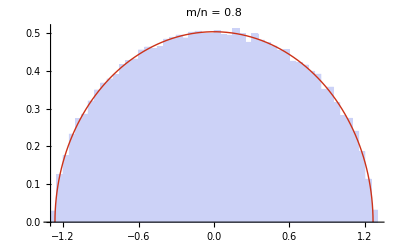

```mathematica
n=300;
m=2/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧),S2,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;

m=4/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧),S4,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;

n=300;
m=8/10 n;
HistogramPlot[(Q=RandomOrthogonal[n];
(Q.RandomSymmetric[n].Transpose[Q])⟦;;m,;;m⟧),S8,PlotLabel->"m/n = "<>ToString[m/n//N]]//Print;
```

We can compare with histograms

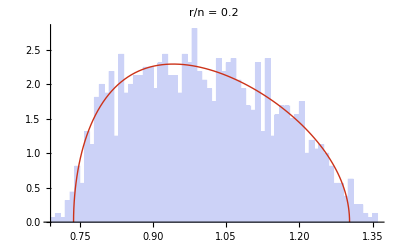

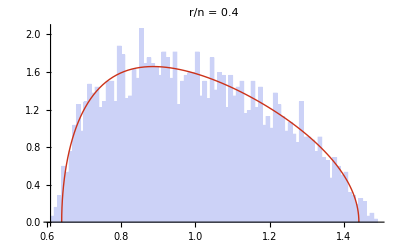

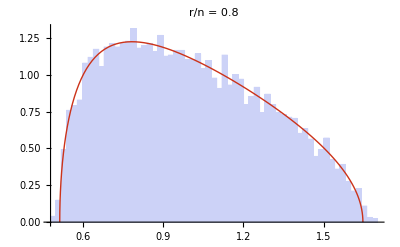

```mathematica
m=80;n=10 m; r=2/10 m;

HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
(Q.A.Transpose[A].Transpose[Q])⟦;;r,;;r⟧),MP2,PlotLabel->"r/n = "<>ToString[r/m//N]]//Print;

r=4/10 m;

HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
(Q.A.Transpose[A].Transpose[Q])⟦;;r,;;r⟧),MP4,PlotLabel->"r/n = "<>ToString[r/m//N]]//Print;

r=8/10 m;

HistogramPlot[(
A=RandomReal[NormalDistribution[0,1],{m,n}]/Sqrt[n];
Q=RandomOrthogonal[m];
(Q.A.Transpose[A].Transpose[Q])⟦;;r,;;r⟧),MP8,PlotLabel->"r/n = "<>ToString[r/m//N]]//Print;
```